# Network Map Animation Routines :: HMSC

## Functions

```mathematica
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]]
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
GraphMap2[{raw_,coordsRaw_,rawPop_,name_,pad_},maxTransitionsSize_,imageSize_,cityScaler_,cityScaler2_]:=Module[{coords,head,data,pops,popsVct,sizes,edgeshape,graph,coordSizePairs,points},
{coords,head,data,pops}={
coordsRaw[[2;;All,2;;All]],
raw[[1]][[2;;All]],
Chop[raw[[2;;All,2;;All]]],
rawPop[[2;;All,2]]
};
(**)
popsVct=Log/@(1+Rescale[#,{Min[pops],Max[pops]/10}]&/@pops//N);
sizes=(ToString[#[[1]]]->(cityScaler*#[[2]]))&/@Transpose[{Range[1,popsVct//Length],popsVct}];
(**)
coordSizePairs=Transpose[{coords,sizes}];
points=Disk[#[[1]],#[[2,2]]/cityScaler2]&/@coordSizePairs;
(*Print[points];
Graphics[points]*)
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]};
graph=GraphTransitionsFrequenciesWithMax[{data,ToString/@Range[data//Length]},maxTransitionsSize,VertexLabelStyle->Opacity[0],
EdgeShapeFunction->edgeshape,
VertexCoordinates->coords,
VertexSize->.00001,
VertexStyle->{{EdgeForm[None],Black}},
ImageSize->imageSize,
LineThickness->.025,
VariableStyle->"LineWidth",
Prolog->Flatten[{EdgeForm[{Black,Thickness[.005]}],White,CountryData["Comoros",{"FullPolygon","Equirectangular"}],Flatten[{Darker[White,1],points}]}],
Epilog->Flatten[{Darker[White,1],points}],
ImagePadding->pad
];
graph
]
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding]
]
]
MapNetworkWithGenotypes[{countryMap_,cityCoordinates_},{transitionsMatrix_,nodeNames_},{nodesShapes_,nodesSizes_},{imageSize_,nodeScaler_,maxTransitionsSize_,padding_,lineWidth_}]:=Module[{},
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]};
GraphTransitionsFrequenciesWithMax[transitionsMatrix,maxTransitionsSize,
VertexLabelStyle->Opacity[0],
EdgeShapeFunction->edgeshape,
VertexCoordinates->cityCoordinates,
VertexSize->nodesSizes,
VertexShape->nodesShapes,
ImageSize->imageSize,
LineThickness->lineWidth,
VariableStyle->"LineWidth",
ImagePadding->padding,
Prolog->Flatten[{EdgeForm[{Black,Thickness[.005]}],White,countryMap}]
]
]
ListLinePlotPopulation[mosyPop_,genotypes_,plotRange_,colors_]:=ListLinePlot[Append[mosyPop//Transpose,Total/@mosyPop],
PlotLegends->Append[genotypes,"Total"],
PlotRange->plotRange,
ImageSize->400,
Frame->True,
FrameStyle->Thick,
GridLines->Automatic,
PlotStyle->(Append[{Opacity[.9],Thickness[.0075]},#]&/@colors),
FrameTicksStyle->Directive[Gray,12],
FrameLabel->(Style[#,20,Black]&/@{"Time","Population"})
]
```

/Users/sanchez.hmsc/Documents/GitHub/MGDrivE/R/ComorosTest

## Static Map Routine

```mathematica
comorosPolygon=CountryData["Comoros",{"FullPolygon","Equirectangular"}];
Graphics[comorosPolygon];
```

```mathematica
largestCities=CountryData["Comoros","LargestCities"];
coordinates=CityData[#,"Coordinates"]&/@largestCities;
populations=CityData[#,"Population"]&/@largestCities;
missing=Position[coordinates,Missing["NotAvailable"]];
cities=(Delete[#,missing]&/@{largestCities[[All,2,1]],coordinates,populations//Normal})//Transpose;
movementMatrix=RandomReal[{0,1},{Length[cities],Length[cities]}];
headedMatrix=Prepend[Prepend[movementMatrix,cities[[All,1]]]//Transpose,Prepend[cities[[All,1]],""]]//Transpose;

{comRawPop,comCoordsRaw,comName,comPad}={
Prepend[Transpose[{Range[Length[cities[[All,3]]]],cities[[All,3]]//Normal}],{"","",""}],
Prepend[Flatten/@Transpose[{Range[Length[cities[[All,2]]]],Reverse/@cities[[All,2]]}],{"","",""}],
"Comoros",
{{0,-100},{0,-100}}
};
```

```mathematica
distancesMatrix=Table[
EuclideanDistance[cities[[i,2]],#]&/@cities[[All,2]]
,{i,1,cities//Length}];
fixed=ReplaceAll[#,ComplexInfinity->0]&/@Quiet[(1/distancesMatrix)];
thresheld=Table[If[#>2,#,0]&/@i,{i,fixed}];
headedMatrix=Prepend[Prepend[thresheld,cities[[All,1]]]//Transpose,Prepend[cities[[All,1]],""]]//Transpose;
map=GraphMap2[{ReplacePart[headedMatrix,{i_,i_}->0]//UpperTriangularize,Transpose[{comCoordsRaw[[All,1]],comCoordsRaw[[All,2]]+.0075,comCoordsRaw[[All,3]] -.0075}],comRawPop,"Comoros",{{50,50},{50,50}}},500,800,.5,100]
(*Export["./Comoros.pdf",map,"ImageEncoding"->"LZW"]*)
```

-Graphics-

## Export

cities.csv

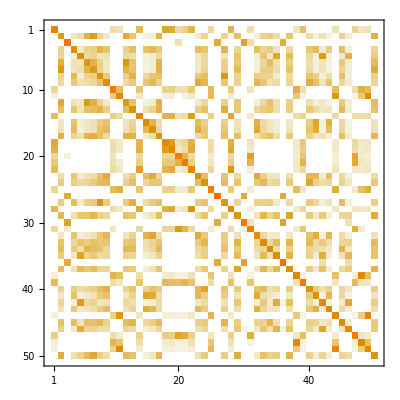

transitions.csv

```mathematica
Export["cities.csv",Flatten/@cities]
transitionsMatrix=(#/Total[#])&/@ReplacePart[thresheld,{i_,i_}->100];
MatrixPlot[transitionsMatrix]
headedMatrix=Prepend[Prepend[transitionsMatrix//UpperTriangularize,cities[[All,1]]]//Transpose,Prepend[cities[[All,1]],""]]//Transpose;
Export["transitions.csv",transitionsMatrix]
```

## Pre - Process Frames (Pie Charts)

```mathematica
dataPath="./CRISPR_Resistant01/";
names=FileNames["ADM_PATCH*.csv",dataPath]//Sort;
dataSets=ParallelMap[Import[#][[2;;All,2;;All]]&,names];
frames=Table[
ParallelMap[{
PieChart[#,ChartStyle->"LakeColors",BaseStyle->Directive[EdgeForm[Thin]],ColorFunction->(EdgeForm[None]&)],
Total[#]
}&,i]
,{i,dataSets[[1;;All]]}];
```

```mathematica
timeFrames=(frames//Transpose);
maxPop=Flatten[(#[[All,2]])&/@timeFrames]//Max;
scaledSizesTimeFrames=Table[{#[[1]],#[[2]]/maxPop}&/@i,{i,timeFrames}];
```

```mathematica
(*tick=1;
scaler=3;
(**)
range=Range[dataSets//Length];
vertexShapes=Flatten[{#[[1]]->#[[2]]}&/@Transpose[{range,scaledSizesTimeFrames[[tick]][[All,1]]}]];
vertexSizes=Flatten[{#[[1]]->scaler*#[[2]]}&/@Transpose[{range,scaledSizesTimeFrames[[tick]][[All,2]]}]];
vertexCoordinates=cities[[All,2]];
transitionsMatrix={thresheld,ToString/@range};
countryMap=CountryData["Comoros",{"FullPolygon","Equirectangular"}];*)
```

## Pre - Process Frames (PopDynamics)

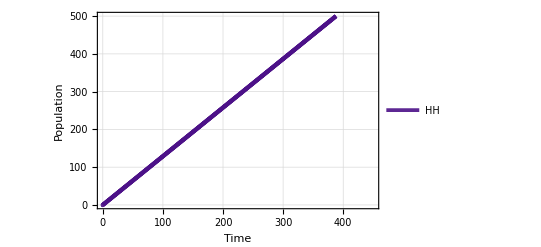

```mathematica
genotypes=Import[names[[1]]][[1,2;;All]];
patch=1;
popDynPlots=Table[
set=dataSets[[patch]][[1;;i]];
llPop=ListLinePlotPopulation[set,genotypes,{{0,450},{0,500}},colors]
,{i,1,Length[dataSets[[1]]]}];
popDynPlots[[400]]
```

## Network Frames

```mathematica
tick=400;
scaler=25;
(**)
range=Range[dataSets//Length];
vertexShapes=Flatten[{ToString[#[[1]]]->#[[2]]}&/@Transpose[{range,scaledSizesTimeFrames[[tick]][[All,1]]}]];
vertexSizes=Flatten[{ToString[#[[1]] ]->scaler*#[[2]]}&/@Transpose[{range,scaledSizesTimeFrames[[tick]][[All,2]]}]];
vertexCoordinates={#[[1]]+.0025,#[[2]]-.09}&/@Reverse/@cities[[All,2]];
transitionsMatrix={thresheld,ToString/@range};
countryMap=CountryData["Comoros",{"FullPolygon","Mercator"}];
(*GRAPH*)
graph=GraphTransitionsFrequenciesWithMax[transitionsMatrix,10,
VertexCoordinates->vertexCoordinates,
VertexShape->vertexShapes,
VertexSize->vertexSizes,
LineThickness->.000075,
VariableStyle->"LineWidth",
VertexLabelStyle->Directive[Red,Italic,Opacity[0]],
ImageSize->1000,
Prolog->Flatten[{EdgeForm[{Black,Opacity[.9],Thickness[.015]}],White,countryMap}],
ImagePadding->{{150,150},{50,50}},
ImageSize->{2560,1600}
]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

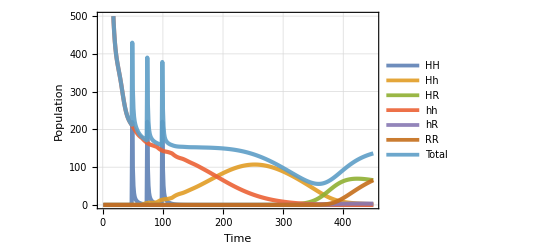
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics-

```mathematica
Overlay[{graph,popDynPlots[[450]]},Alignment->Right]
```

```mathematica
(**)
range=Range[dataSets//Length];
transitionsMatrix={thresheld,ToString/@range};
countryMap=CountryData["Comoros",{"FullPolygon","Mercator"}];
Table[
tick=i;
scaler=30;
(**)
vertexShapes=Flatten[{ToString[#[[1]]]->#[[2]]}&/@Transpose[{range,scaledSizesTimeFrames[[tick]][[All,1]]}]];
vertexSizes=Flatten[{ToString[#[[1]] ]->scaler*#[[2]]}&/@Transpose[{range,scaledSizesTimeFrames[[tick]][[All,2]]}]];
vertexCoordinates={#[[1]]+.0025,#[[2]]-.09}&/@Reverse/@cities[[All,2]];
(*GRAPH*)
graph=GraphTransitionsFrequenciesWithMax[transitionsMatrix,10,
VertexCoordinates->vertexCoordinates,
VertexShape->vertexShapes,
VertexSize->vertexSizes,
LineThickness->.000075,
VariableStyle->"LineWidth",
VertexLabelStyle->Directive[Red,Italic,Opacity[0]],
ImageSize->1000,
Prolog->Flatten[{EdgeForm[{Black,Opacity[.9],Thickness[.015]}],White,countryMap}],
ImagePadding->{{150,150},{50,50}}
];
Export[NotebookDirectory[]<>"/Frames/graph"<>StringPadLeft[ToString[i],5,"0"]<>".png",graph,ImageResolution->500,ImageSize->{2560,1600}];
,{i,1,2}];
```

```mathematica
GenerateExportNetworkFrame[pieCharts_,popSizes_,range_,countryMap_,frameNumber_]:=Module[{vertexShapes,vertexSizes,vertexCoordinates,graph},
(**)
vertexShapes=Flatten[{ToString[#[[1]]]->#[[2]]}&/@Transpose[{range,pieCharts}]];
vertexSizes=Flatten[{ToString[#[[1]] ]->scaler*#[[2]]}&/@Transpose[{range,popSizes}]];
vertexCoordinates={#[[1]]+.0025,#[[2]]-.09}&/@Reverse/@cities[[All,2]];
(*GRAPH*)
graph=GraphTransitionsFrequenciesWithMax[transitionsMatrix,10,
VertexCoordinates->vertexCoordinates,
VertexShape->vertexShapes,
VertexSize->vertexSizes,
LineThickness->.000075,
VariableStyle->"LineWidth",
VertexLabelStyle->Directive[Red,Italic,Opacity[0]],
ImageSize->1000,
Prolog->Flatten[{EdgeForm[{Black,Opacity[.9],Thickness[.015]}],White,countryMap}],
ImagePadding->{{150,150},{50,50}}
]
]
```

## Tests

```mathematica
frequencies[[2]]
```

{0,0,0,6.40184,7.17958,35.3553,100.,9.40721,6.14295,0,0,44.7214,14.1421,0,4.28746,5.44735,27.735,0,0,0,0,0,5.85206,9.05357,0,0,10.1015,0,17.6777,0,0,5.07673,10.1535,11.7041,7.98087,0,13.8675,0,0,7.66965,4.74045,6.86803,4.04888,0,9.80581,5.72598,0,0,0,35.3553}

```mathematica
sizeList=(ToString[#[[1]]]->#[[2]])&/@vertexSizes
```

{1→0.954998,2→1.46043,3→1.13433,4→0.895553,5→1.19114,6→1.28505,7→1.49938,8→1.37407,9→1.09034,10→0.707953,11→1.32612,12→1.42398,13→1.22358,14→1.15311,15→0.983503,16→1.24488,17→1.25505,18→1.31388,19→1.40835,20→1.22067,21→0.862801,22→1.52321,23→1.22124,24→1.20194,25→0.724251,26→0.836023,27→1.39947,28→1.46137,29→1.24178,30→1.44369,31→1.01672,32→1.2386,33→1.01856,34→0.799422,35→1.02165,36→1.04031,37→1.13774,38→1.29616,39→0.705215,40→1.17819,41→1.16777,42→1.16646,43→0.793192,44→1.38152,45→0.903219,46→0.834153,47→0.995683,48→1.26292,49→1.58645,50→1.26847}

```mathematica
frequencies=transitionsMatrix[[1]];
max=1;
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[range]},{j,Length[range]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequencies[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->.00001,VariableStyle->"LineWidth"];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
graph=Graph[frequencies,links,EdgeStyle->edgesStyleList]
```

-Graphics-

```mathematica
AbsoluteOptions[graph];
```

```mathematica
edgesStyleList
```

{0.->0.→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.0000353333]},0.->0.→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.0000290988]},0.->0.→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.0000971286]},0.->0.→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.00027735]},0.->0.→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.0002]},0.->0.→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.0000360609]},1067,35.3553->4.74045→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.0000485071]},35.3553->6.86803→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.0000821995]},35.3553->4.04888→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.0000421825]},35.3553->9.80581→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.0000833333]},35.3553->5.72598→{Opacity[0.5],RGBColor[0, 0, 1],Thickness[0.0000660819]}}
 |  |  |  |

```mathematica
transFixed=(#/Total[#])&/@(transitionsMatrix[[1]]);
AdjacencyGraph[Round/@(transitionsMatrix[[1]]),VertexSize->vertexSizes,VertexShape->vertexShapes,VertexCoordinates->vertexCoordinates,ImageSize->500]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-